# 4基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

グラフ分析部分のみ、save済みグラフを読み込む。

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.908450549239282×10^9

#### 変数

```mathematica
date="20230920"
```

20230920

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci.P~5"
base["cs"]="T=cs.R=.P="
base["la"]="T=la.T~ea.A~hc.A~go.A~bot.P~api"
base["wk"]="T=wk.P~4.A~bot"
base["all"]="T=4"
```

T=ci.P~5

T=cs.R=.P=

T=la.T~ea.A~hc.A~go.A~bot.P~api

T=wk.P~4.A~bot

T=4

```mathematica
mountdir="/Volumes/IODATA/NII/togo-log/rcoslogs/"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20230920.rcoslog0003.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20230920.rcoslog0003.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

16260867 217713283 7711269280 log-20230920.rcoslog0003.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## Analysis

#### Get graph

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230920/T=4/_story

```mathematica
Get[savedir<>"/storyGrIdxFlDs3.save"];
```

#### Analysis 1

基本属性

エッジ:

```mathematica
(eltbl[4]=Table[EdgeList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{174349}

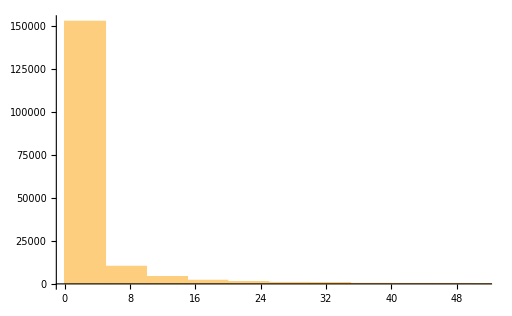

```mathematica
Histogram[Map[Length,eltbl[4]],{5}]
```

ノード:

```mathematica
(vltbl[4]=Table[VertexList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{174349}

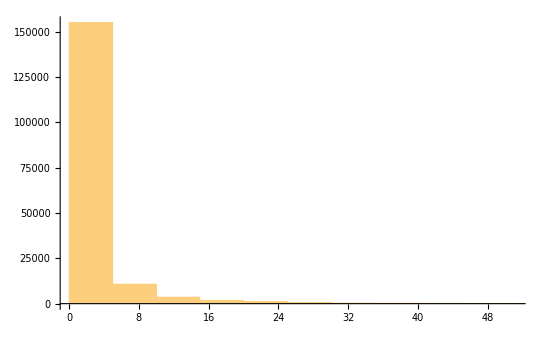

```mathematica
Histogram[Map[Length,vltbl[4]],{5}]
```

アクセス時刻:

```mathematica
(acct[4]=Map[#[[3,1]]&,eltbl[4],{2}])//Dimensions
```

{174349}

滞留時間：

```mathematica
(accspanMin[4]=Map[Max[#]-Min[#]&,acct[4]]/60)//Dimensions
```

{174349}

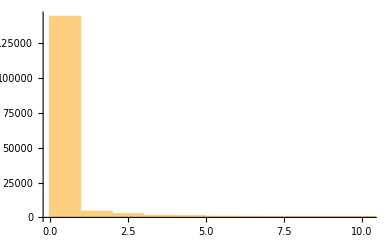

```mathematica
Histogram[accspanMin[4],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[4]=Map[Length,eltbl[4]]/Map[Length,vltbl[4]]//N)//Dimensions
```

{174349}

TV ratio :

```mathematica
(ratioTV[4]=acct[4]/Map[Length,vltbl[4]])//Dimensions
```

{174349}

TE ratio:

```mathematica
(ratioTE[4]=acct[4]/Map[Length,eltbl[4]])//Dimensions
```

{174349}

#### Analysis 2

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[4]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[4]])//Dimensions
```

Part::partw: Part {1,3} of {cir.nii.ac.jp} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{174349}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[4]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{39,40,46,187,202,231,232,235,269,271,304,331,332,378,379,416,423,572,654,662,745,752,783,785,786,996,997,1028,1354}

```mathematica
(Flatten[GrBases[4]]//Union)[[niidnpos]]
```

{http:ci.nii.ac.jp,http:cir.nii.ac.jp,http:dsr.nii.ac.jp,https:auth.cir.nii.ac.jp,https:binder.cs.rcos.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:cir.nii.ac.jp,https:doshisha.repo.nii.ac.jp,https:ds.gakunin.nii.ac.jp,https:feedback.cir.nii.ac.jp,https:ge.nii.ac.jp,https:ge.nii.ac.jp:443,https:idp.nii.ac.jp,https:idp.rdm.nii.ac.jp,https:jupyter.cs.rcos.nii.ac.jp,https:kaken.nii.ac.jp,https:lms.nii.ac.jp,https:nrid.nii.ac.jp,https:office.gakunin.nii.ac.jp,https:openidp.nii.ac.jp,https:otsuma.repo.nii.ac.jp,https:rcos.nii.ac.jp,https:rdm.nii.ac.jp,https:redmine.devops.rcos.nii.ac.jp,https:support.irdb.nii.ac.jp,https:support.nii.ac.jp,https:toyo.repo.nii.ac.jp,https:www.nii.ac.jp}

```mathematica
(GrNiiBases[4]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[".*\\.nii.ac.jp.*"]]||StringMatchQ[x,RegularExpression[".*\\.jdcat.jsps.go.jp.*"]]]&,GrBases[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*\.jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{174349}

```mathematica
Map[Length,GrBases[4]]//Tally
```

{{2,159395},{1,14950},{3,4}}

```mathematica
Map[Length,GrNiiBases[4]]//Tally
```

{{1,113620},{2,60661},{0,68}}

```mathematica
(GrBasesTly[4]=Tally[ GrBases[4]])//Dimensions
```

{1573,2}

```mathematica
(GrNiiBasesTly[4]= Tally[GrNiiBases[4]])//Dimensions
```

{35,2}

```mathematica
TableForm[GrNiiBasesTly[4]]
```

https:cir.nii.ac.jp | 112928
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 24688
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 35145
https:lms.nii.ac.jp | 609
https:ds.gakunin.nii.ac.jp
https:lms.nii.ac.jp | 1
https:jupyter.cs.rcos.nii.ac.jp
https:rdm.nii.ac.jp | 16
https:jupyter.cs.rcos.nii.ac.jp
https:openidp.nii.ac.jp | 9
https:jupyter.cs.rcos.nii.ac.jp | 82
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 136
https:cir.nii.ac.jp
https:lms.nii.ac.jp | 4
 | 68
https:cir.nii.ac.jp
https:support.nii.ac.jp | 92
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 3
https:cir.nii.ac.jp
https:www.nii.ac.jp | 6
https:cir.nii.ac.jp
https:kaken.nii.ac.jp | 329
https:cir.nii.ac.jp
https:nrid.nii.ac.jp | 195
https:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 7
https:idp.rdm.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 5
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 7
https:cir.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:lms.nii.ac.jp
https:rcos.nii.ac.jp | 1
https:idp.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 2
https:cir.nii.ac.jp
https:office.gakunin.nii.ac.jp | 2
https:cir.nii.ac.jp
https:toyo.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:otsuma.repo.nii.ac.jp | 1
https:idp.nii.ac.jp
https:lms.nii.ac.jp | 1
https:redmine.devops.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:feedback.cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp | 2
https:cir.nii.ac.jp
https:doshisha.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:support.irdb.nii.ac.jp | 1
http:dsr.nii.ac.jp
https:cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp:443 | 1
https:lms.nii.ac.jp
https:www.nii.ac.jp | 1

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

#### Analysis 3 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP[4]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{174349}

```mathematica
(ckanGrR[4]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{174349}

```mathematica
(ckanGrPR[4]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{174349}

```mathematica
(ckanGrPsel[4]=Cases[ckanGrP[4],{__},{1}])//Dimensions
```

{79,3}

```mathematica
ckanGrPselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
ckanGrPselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
(ckanGrRsel[4]=Cases[ckanGrR[4],{__},{1}])//Dimensions
```

{13,3}

```mathematica
ckanGrRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
ckanGrRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
(ckanGrPRsel[4]=Cases[ckanGrPR[4],{__},{1}])//Dimensions
```

{80,3}

```mathematica
ckanGrPRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
ckanGrPRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
(ckanGrPRselHL[4]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel[4]])//Dimensions
```

{80,3}

```mathematica
ckanGrPRVcount[4]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL[4]]
```

{28,2,5,2,11,2,2,3,4,2,11,11,6,5,13,6,23,5,19,9,12,46,23,5,11,38,36,33,78,85,79,13,11,2,44,37,37,9,4,6,20,19,3,24,17,14,7,2,282,294,283,283,34,8,83,85,83,83,83,53,67,81,80,4,32,2,2,45,24,22,23,2,29,2,10,14,2,6,2,36}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime[4]=Map[stayTime[#[[3]]]&,ckanGrPRselHL[4]]
```

{15270.,0.,65.,0.,10046.,0.,0.,5.,100.,0.,8259.,8197.,160.,85.,161.,5483.,34780.,8134.,1311.,611.,428.,7589.,1035.,110.,4473.,1858.,1833.,1080.,17190.,22589.,17180.,809.,1562.,0.,24163.,24163.,24163.,13825.,593.,1461.,2308.,2163.,11.,26428.,11187.,2256.,327.,0.,24190.,36703.,24190.,24190.,30078.,41639.,27334.,27327.,27327.,27327.,27327.,13449.,24755.,3036.,3006.,165.,24972.,0.,0.,640.,21768.,21364.,21364.,0.,27577.,0.,196.,225.,0.,196.,0.,29591.}

#### Analysis 4 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,Sqrt];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
(ckanGrPRselHLAT[4]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL[4]])//Dimensions
```

{80,3}

ロググループ：

```mathematica
loggroupCKAN=Map[#[[2]]&,ckanGrPRselHLAT[4]]
```

{{1582,1},{2630,1},{4033,1},{7218,1},{11954,1},{12855,1},{13250,1},{17687,1},{18075,1},{18456,1},{21851,1},{21851,1},{23265,1},{24605,1},{25891,1},{30251,1},{33733,1},{34989,1},{39200,1},{47383,1},{50683,1},{50975,1},{54675,1},{56091,1},{56419,1},{57734,1},{57734,1},{58352,1},{59762,1},{59762,1},{59762,1},{61185,1},{64737,1},{66206,1},{68858,1},{68858,1},{68858,1},{69200,1},{70069,1},{70072,1},{70085,1},{70085,1},{70085,1},{70287,1},{70287,1},{70287,1},{73453,1},{80381,1},{85869,1},{85869,1},{85869,1},{85869,1},{86652,1},{86652,1},{86701,1},{86701,1},{86701,1},{86701,1},{86701,1},{87037,1},{87037,1},{87202,1},{87202,1},{88530,1},{91386,1},{91473,1},{94925,1},{94987,1},{95450,1},{95450,1},{95450,1},{95892,1},{99273,1},{99804,1},{101757,1},{137786,1},{139273,1},{142307,1},{143592,1},{144328,1}}

ノードの数え上げ：

```mathematica
vcCKAN=Map[VertexCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{28,2,5,2,11,2,2,3,4,2,11,11,6,5,13,6,23,5,19,9,12,46,23,5,11,38,36,33,78,85,79,13,11,2,44,37,37,9,4,6,20,19,3,24,17,14,7,2,282,294,283,283,34,8,83,85,83,83,83,53,67,81,80,4,32,2,2,45,24,22,23,2,29,2,10,14,2,6,2,36}

エッジの数え上げ：

```mathematica
ecCKAN=Map[EdgeCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{62,1,5,1,18,1,1,3,4,1,19,19,8,5,16,5,31,5,36,12,19,85,24,6,17,65,63,46,124,135,113,21,17,1,49,44,44,9,3,8,30,26,2,35,26,20,10,1,436,457,438,454,4,7,138,144,137,133,136,68,90,164,154,3,56,1,1,132,70,56,57,1,44,1,19,17,1,7,1,33}

アクセス時刻：

```mathematica
(accCKAN=Map[Map[#[[3,1]]&,EdgeList[#[[3]]]]&,ckanGrPRselHLAT[4]])//Dimensions
```

{80}

最大滞在時間：

```mathematica
maxTimeSpan[l_]:=Max[Map[#[[1]]-#[[2]]&,Partition[Sort[l,#1>#2&],2,1]]]
```

```mathematica
(maxtimespanCKAN=Map[maxTimeSpan,accCKAN]/.{-Infinity->0})/60
```

{244.15,0,0.733333,0,139.133,0,0,0.0666667,1.53333,0,134.517,134.517,0.866667,0.616667,0.683333,90.9167,557.45,71.1667,15.45,6.71667,2.7,65.1833,6.43333,0.7,53.6333,8.66667,8.66667,1.28333,51.8667,82.6333,57.1333,4.38333,12.8833,0,139.433,139.433,139.433,83.8833,9.8,23.5667,7.13333,7.13333,0.183333,326.65,148.5,35.1667,3.21667,0,62.1,60.8,62.1,62.1,494.117,413.,113.717,67.8833,113.717,113.717,113.717,174.7,173.65,6.7,8.58333,1.43333,207.233,0,0,0.933333,137.633,168.933,168.933,0,274.367,0,0.816667,0.766667,0,1.3,0,256.217}

滞留時間：

```mathematica
staytimeCKAN=Map[Max[#]-Min[#]&,accCKAN]
```

{15270.,0.,65.,0.,10046.,0.,0.,5.,100.,0.,8259.,8197.,160.,85.,161.,5483.,34780.,8134.,1311.,611.,428.,7589.,1035.,110.,4473.,1858.,1833.,1080.,17190.,22589.,17180.,809.,1562.,0.,24163.,24163.,24163.,13825.,593.,1461.,2308.,2163.,11.,26428.,11187.,2256.,327.,0.,24190.,36703.,24190.,24190.,30078.,41639.,27334.,27327.,27327.,27327.,27327.,13449.,24755.,3036.,3006.,165.,24972.,0.,0.,640.,21768.,21364.,21364.,0.,27577.,0.,196.,225.,0.,196.,0.,29591.}

```mathematica
staytimeCKAN/60
```

{254.5,0.,1.08333,0.,167.433,0.,0.,0.0833333,1.66667,0.,137.65,136.617,2.66667,1.41667,2.68333,91.3833,579.667,135.567,21.85,10.1833,7.13333,126.483,17.25,1.83333,74.55,30.9667,30.55,18.,286.5,376.483,286.333,13.4833,26.0333,0.,402.717,402.717,402.717,230.417,9.88333,24.35,38.4667,36.05,0.183333,440.467,186.45,37.6,5.45,0.,403.167,611.717,403.167,403.167,501.3,693.983,455.567,455.45,455.45,455.45,455.45,224.15,412.583,50.6,50.1,2.75,416.2,0.,0.,10.6667,362.8,356.067,356.067,0.,459.617,0.,3.26667,3.75,0.,3.26667,0.,493.183}

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

```mathematica
(ckanGrPRselHLTL[4]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT[4]])//Dimensions
```

Part::partd: Part specification https://search.yahoo.co.jp/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.google.com/⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{80}

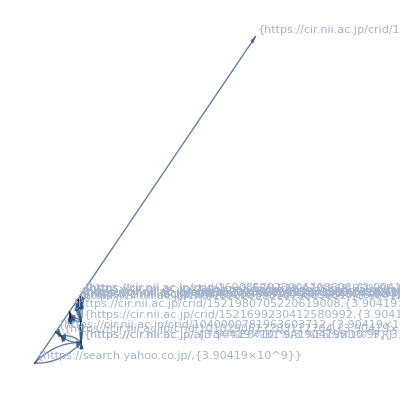
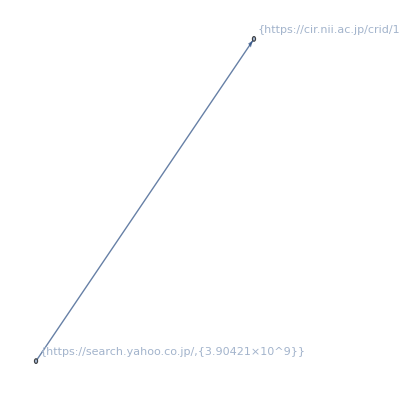
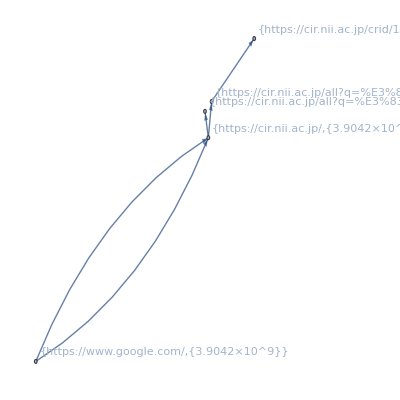
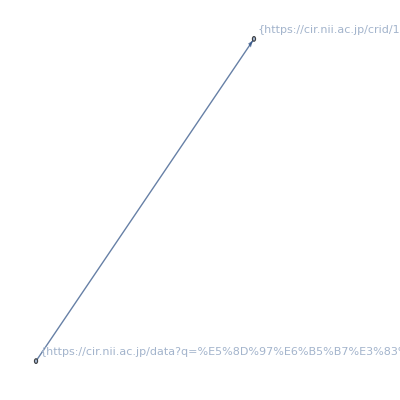
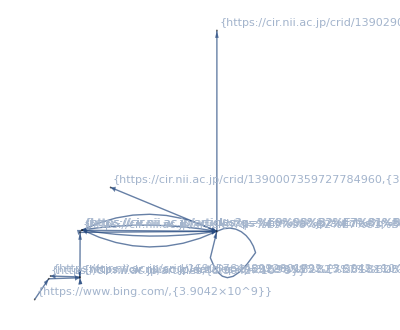
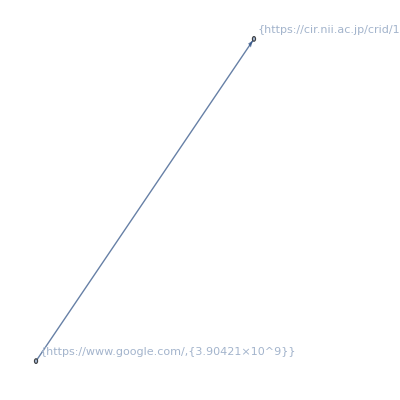
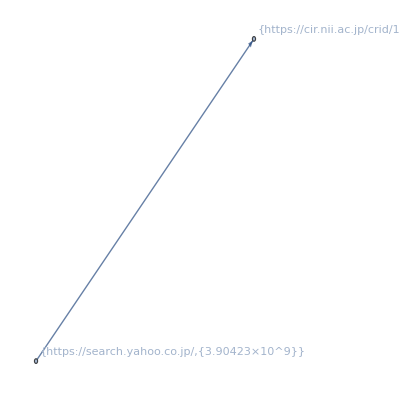
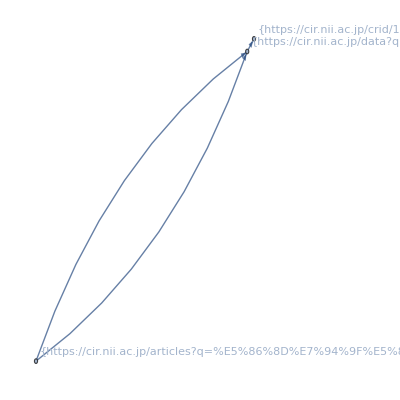
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
ckanGrPRselHLTL[4]//TableForm
```

#### Report:CKAN impact

```mathematica
logtbl={{"- ログ件数 -","述べログ件数"},{{"全件数","ユーザーアクセス件数"},{ToExpression[StringSplit[logwc][[1]]],idxLogLen[4]}}}//TableForm
```

- ログ件数 - | 述べログ件数
全件数
ユーザーアクセス件数 | 16260867
3257953

```mathematica
ckanlogtbl={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},{{"リクエストにCKAN-crid含む","リファラーにCKAN-crid含む","いずれか含む"},{ckanCridPLogPos[4]//Length,ckanCridRLogPos[4]//Length,ckanCridPRLogPos[4]//Length},{Union[ckanCridPlist]//Length,Union[ckanCridRlist]//Length,ckanCridPRU//Length}}}//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む
リファラーにCKAN-crid含む
いずれか含む | 221
13
234 | 207
9
207

```mathematica
ckanchaintbl={{"- アクション連鎖数 -","件数"},{{"全件数","ノードにCKAN-crid含む"},{storyGrIdxFlDs3[4]//Length,ckanGrPRselHL[4]//Length}}}//TableForm
```

- アクション連鎖数 - | 件数
全件数
ノードにCKAN-crid含む | 174349
80

```mathematica
ckangrsummarytbl={{"アクセスグラフ通し番号","ロググループ","ノード数","エッジ数","最大飛躍時間(分)","滞留時間(分)"},{Table[i,{i,Length[loggroupCKAN]}],loggroupCKAN,vcCKAN,ecCKAN,maxtimespanCKAN/60,staytimeCKAN/60}}//TableForm
```

アクセスグラフ通し番号 | ロググループ | ノード数 | エッジ数 | 最大飛躍時間(分) | 滞留時間(分)
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80 | 1582 | 1
2630 | 1
4033 | 1
7218 | 1
11954 | 1
12855 | 1
13250 | 1
17687 | 1
18075 | 1
18456 | 1
21851 | 1
21851 | 1
23265 | 1
24605 | 1
25891 | 1
30251 | 1
33733 | 1
34989 | 1
39200 | 1
47383 | 1
50683 | 1
50975 | 1
54675 | 1
56091 | 1
56419 | 1
57734 | 1
57734 | 1
58352 | 1
59762 | 1
59762 | 1
59762 | 1
61185 | 1
64737 | 1
66206 | 1
68858 | 1
68858 | 1
68858 | 1
69200 | 1
70069 | 1
70072 | 1
70085 | 1
70085 | 1
70085 | 1
70287 | 1
70287 | 1
70287 | 1
73453 | 1
80381 | 1
85869 | 1
85869 | 1
85869 | 1
85869 | 1
86652 | 1
86652 | 1
86701 | 1
86701 | 1
86701 | 1
86701 | 1
86701 | 1
87037 | 1
87037 | 1
87202 | 1
87202 | 1
88530 | 1
91386 | 1
91473 | 1
94925 | 1
94987 | 1
95450 | 1
95450 | 1
95450 | 1
95892 | 1
99273 | 1
99804 | 1
101757 | 1
137786 | 1
139273 | 1
142307 | 1
143592 | 1
144328 | 1 | 28
2
5
2
11
2
2
3
4
2
11
11
6
5
13
6
23
5
19
9
12
46
23
5
11
38
36
33
78
85
79
13
11
2
44
37
37
9
4
6
20
19
3
24
17
14
7
2
282
294
283
283
34
8
83
85
83
83
83
53
67
81
80
4
32
2
2
45
24
22
23
2
29
2
10
14
2
6
2
36 | 62
1
5
1
18
1
1
3
4
1
19
19
8
5
16
5
31
5
36
12
19
85
24
6
17
65
63
46
124
135
113
21
17
1
49
44
44
9
3
8
30
26
2
35
26
20
10
1
436
457
438
454
4
7
138
144
137
133
136
68
90
164
154
3
56
1
1
132
70
56
57
1
44
1
19
17
1
7
1
33 | 244.15
0
0.733333
0
139.133
0
0
0.0666667
1.53333
0
134.517
134.517
0.866667
0.616667
0.683333
90.9167
557.45
71.1667
15.45
6.71667
2.7
65.1833
6.43333
0.7
53.6333
8.66667
8.66667
1.28333
51.8667
82.6333
57.1333
4.38333
12.8833
0
139.433
139.433
139.433
83.8833
9.8
23.5667
7.13333
7.13333
0.183333
326.65
148.5
35.1667
3.21667
0
62.1
60.8
62.1
62.1
494.117
413.
113.717
67.8833
113.717
113.717
113.717
174.7
173.65
6.7
8.58333
1.43333
207.233
0
0
0.933333
137.633
168.933
168.933
0
274.367
0
0.816667
0.766667
0
1.3
0
256.217 | 254.5
0.
1.08333
0.
167.433
0.
0.
0.0833333
1.66667
0.
137.65
136.617
2.66667
1.41667
2.68333
91.3833
579.667
135.567
21.85
10.1833
7.13333
126.483
17.25
1.83333
74.55
30.9667
30.55
18.
286.5
376.483
286.333
13.4833
26.0333
0.
402.717
402.717
402.717
230.417
9.88333
24.35
38.4667
36.05
0.183333
440.467
186.45
37.6
5.45
0.
403.167
611.717
403.167
403.167
501.3
693.983
455.567
455.45
455.45
455.45
455.45
224.15
412.583
50.6
50.1
2.75
416.2
0.
0.
10.6667
362.8
356.067
356.067
0.
459.617
0.
3.26667
3.75
0.
3.26667
0.
493.183

```mathematica
(ckanEL=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL[4]])//Dimensions
```

{80}

```mathematica
expdir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230920/T=4/_story

```mathematica
SetDirectory[expdir]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230920/T=4/_story

```mathematica
(*Export["ckanedgelist.json",exp]*)
```

```mathematica
Sort[Map[#[[3,2]]&,EdgeList[ckanGrPRselHLTL[4][[36]]]]]==Sort[Map[#[[3,2]]&,EdgeList[ckanGrPRselHLTL[4][[37]]]]]
```

False

```mathematica
Sort[Map[#[[3,2]]&,EdgeList[ckanGrPRselHLTL[4][[36]]]]]
```

{819000,819002,819003,819004,819005,819006,819007,819008,819010,819011,819012,819013,819014,819015,819016,819025,819026,819027,819028,819029,819034,819038,819039,819040,819041,819042,819043,819044,819045,819046,819047,819048,819049,819050,819060,819062,819063,819064,819065,819066,819069,819070,819071,819072}

```mathematica
Map[#[[3,2]]&,EdgeList[ckanGrPRselHLTL[4][[37]]]]
```

{819046,819045,819047,819038,819044,819042,819039,819041,819048,819037,819000,819008,819002,819034,819043,819040,819049,819005,819007,819003,819060,819050,819006,819013,819010,819012,819004,819014,819062,819011,819015,819063,819016,819064,819025,819065,819026,819066,819027,819069,819029,819070,819071,819072}

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.908431251736225×10^9

```mathematica
end-start
```

55.18911